```mathematica
(*longks={{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3},{4,0},{3,1},{2,2},{1,3},{0,4},{5,0},{4,1},{3,2},{2,3},{1,4},{0,5},{6,0},{5,1},{4,2},{3,3},{2,4},{1,5},{0,6},{7,0},{6,1},{5,2},{4,3},{3,4},{2,5},{1,6},{0,7},{7,1},{6,2},{5,3},{3,5},{2,6},{1,7},{7,2},{6,3},{3,6},{2,7},{7,3},{3,7}};
<<ToMatlab`
Table[SetPrecision[momRRd[longks[[i,1]],longks[[i,2]]],40],{i,1,Length[longks]}]//ToMatlab;*)
```

```mathematica
ClearAll["Global`*"];

pow[x_,0]:=1/;x==0||x==0.
pow[x_,y_:0]:=x^y
```

```mathematica
(* Physical parameters *)
(*Ca=1;Cp=-1;γ=1;Rey=10 10^6;*)
(*γ=1/2;Rey=4;*)
(* Linear *)
(*Ca=1/2;Cp=1;γ=1;Rey=Infinity;*)
(* RPE *)
Ca=1/2;Cp=1/0.3;γ=1;Rey=Infinity;

μR=1.;
σR=0.1;
μRd=10^-14;
σRd=0.1;
𝒟r=LogNormalDistribution[Log[μR],σR];
𝒟v=NormalDistribution[μRd,σRd];
RRdPDF=ProductDistribution[𝒟r,𝒟v];
momRRd[i_,j_]:=Moment[RRdPDF,{i,j}];

nr=3;
nrd=3;
ks={{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{0,3},{4,0},{0,4}};
(*Flatten[{Table[{q,p},{q,0,nr-1},{p,0,2nrd-1}],
Table[{q,p},{q,nr,2nr-1},{p,0,0}]}
,2];*)

project[xix_,xiy_,w_]:=Module[{moms,mom},
	mom[p_,q_]:=Sum[w[[i]] xix[[i]]^p xiy[[i]]^q,{i,nr nrd}];
	moms=Table[mom[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
	moms
];

hyqmom[momin_]:=Module[{moms=momin,etasmall,verysmall,realizable,realsmall,qmax,n,u,bu,d2,d3,d4,c2,c3,c4,q,eta,slope,det,qp,qm,scales,srho,err,mo,scale,dem,prod,rho,ups,up},
etasmall=10^-10;
verysmall=10^-14;
realsmall=10^-14;
qmax=0.3;
(* check for zero density *)
n=Table[0,{i,3}];u=n;
If[moms[[1]]≤ verysmall,
	n[[2]]=moms[[1]];
	Return[{n,u},Module];
];
(* mean velocities *)
bu=moms[[2]]/moms[[1]];
(* normalized velocities *)
d2=moms[[3]]/moms[[1]];
d3=moms[[4]]/moms[[1]];
d4=moms[[5]]/moms[[1]];
(* central moments *)
c2=d2-bu^2;
c3=d3-3*bu d2+2 bu^3;
c4=d4-4*bu d3+6 bu^2 d2-3 bu^4;
(* realizability check *)
realizable=c2 c4-c2^3-c3^2;
If[c2<0,
	If[c2<-verysmall,
		Print["c2 negative in three node hyqmom"];
		Abort[];
	];
	c2=0;
	c3=0;
	c4=0;
	,
	If[realizable<0,
		If[c2≥ etasmall,
			q=c3/Sqrt[c2]/c2;
			eta=c4/c2/c2;
			If[Abs[q]>verysmall,
				slope=(eta-3)/q;
				det=8+slope^2;
				qp=0.5(slope+Sqrt[det]);
				qm=0.5(slope-Sqrt[det]);
				If[Sign[q]==1,q=qp,q=qm];
			,q=0;
			];
			eta=q^2+1;
			c3=q Sqrt[c2]c2;
			c4=eta c2^2;
			If[realizable<-10^-6,
				Print["c4 too small in three node hyqmom"];
				Abort[];
			];
		,
		c3=0;
		c4=c2^2;
		];
	];
];
(* HyQMOM parameters (scaled) *)
scale=Sqrt[c2];
If[c2≥etasmall,
	q=c3/Sqrt[c2]/c2;
	eta=c4/c2/c2;
	,
	q=0;
	eta=1;
];
(* bound skewness < qmax *)
If[q^2>qmax^2,
	slope=(eta-3)/q;
	q=qmax Sign[q];
	eta=3+slope q;
	realizable=eta-1-q^2;
	If[realizable<0,eta=1+q^2];
];
ups[1]=(q-Sqrt[4 eta-3 q^2])/2;
ups[2]=0;
ups[3]=(q+Sqrt[4 eta-3 q^2])/2;
dem=1/Sqrt[4 eta-3 q^2];
prod=-ups[1]ups[3];
prod=Max[prod,1+realsmall];
rho[1]=-dem/ups[1];
rho[2]=1-1/prod;
rho[3]=dem/ups[3];
(* return exact moment 0,1,2 *)
srho=Sum[rho[i],{i,3}];
Do[rho[i]=rho[i]/srho,{i,3}];
scales=Sum[rho[i] ups[i]^2,{i,3}]/Sum[rho[i],{i,3}];
Do[up[i]=ups[i] scale/Sqrt[scales],{i,3}];
(* error checking *)
If[Min[Table[rho[i],{i,3}]]<0,
	Print["Negative weight in HyQMOM"];
	Abort[];
];
n[[1]]=rho[1];
n[[2]]=rho[2];
n[[3]]=rho[3];
n=moms[[1]]n;
u[[1]]=up[1];
u[[2]]=up[2];
u[[3]]=up[3];
u=bu+u;
(* check moment error *)
mo=Table[Sum[n[[i]]pow[u[[i]],j],{i,1,3}],{j,0,4}];
err=mo-moms;
If[err[[3]]>10^-6&&moms[[1]]>verysmall,
	Print["err ",err];
];
{n,u}
];

chyqmom[momin_]:=Module[{moms=momin,vars,linsolv,mymom,n,csmall,verysmall,bu,bv,d20,d11,d02,d30,d03,d40,d04,c20,c11,c02,c30,c03,c40,c04,M1,rho,up,Vf,M2,rho2,up2,vp21,vp22,vp23,rho21,rho22,rho23,mu2avg,mu2,mu3,mu4,u,v,eqns,pm,q,eta,slope,det,qm,qp,up3,M3,rh3},
	(* pointer *)
	eqns=Table[moms[[i]]==pm[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
	vars=DeleteDuplicates[Flatten[Table[pm[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}]]];
	linsolv=First[vars/.Solve[eqns,vars]];
	mymom[q_,p_]:=linsolv[[First[First[Position[ks,{q,p}]]]]];

	n=Table[0,{i,9}];u=n;v=n;
	csmall=10^-10;
	verysmall=10^-14;
	(* mean velocities *)
	bu=mymom[1,0]/mymom[0,0];
	bv=mymom[0,1]/mymom[0,0];
	(* normalized moments *)
	d20=mymom[2,0]/mymom[0,0];
	d11=mymom[1,1]/mymom[0,0];
	d02=mymom[0,2]/mymom[0,0];
	d30=mymom[3,0]/mymom[0,0];
	d03=mymom[0,3]/mymom[0,0];
	d40=mymom[4,0]/mymom[0,0];
	d04=mymom[0,4]/mymom[0,0];
	(*central moments*)
	c20=d20-bu^2;
	c11=d11-bu bv;
	c02=d02-bv^2;
	c30=d30-3 bu d20+2 bu^3;
	c03=d03-3bv d02+2 bv^3;
	c40=d40-4bu d30+6 bu^2 d20-3 bu^4;
	c04=d04-4bv d03+6 bv^2 d02-3 bv^4;
	(* 3 node hyqmom with realizability checking *)
	M1={1,0,c20,c30,c40};
	{rho,up}=hyqmom[M1];
	(* check c20 = 0 for degenerate case with 1 node in u direction *)
	If[c20≤ csmall,
		rho[[1]]=0;
		rho[[2]]=1;
		rho[[3]]=0;
		Vf = 0 up;
		M2={1,0,c02,c03,c04};
		{rho2,up2}=hyqmom[M2];
		vp21=up2[[1]];
		vp22=up2[[2]];
		vp23=up2[[3]];
		rho21=rho2[[1]];
		rho22=rho2[[2]];
		rho23=rho2[[3]];
	,
		(* HyQMOM - condition on u direction with c20 > 0 *)
		Vf=c11 up/c20;
		(* find conditional variance *)
		mu2avg=c02-Total[rho Vf^2];
		mu2avg=Max[mu2avg,0];
		mu2=mu2avg;mu3=0 mu2;mu4=mu2^2;
		If[mu2>csmall,
			(* 3rd order moment *)
			q=(c03-Total[rho Vf^3])/mu2^(3/2);
			(* 4th order moment with realizability check *)
			eta=(c04-Total[rho Vf^4]-6 Total[rho Vf^2] mu2)/mu2^2;
			(* revert to QMOM if needed *)
			If[eta<q^2+1,
				If[Abs[q]>verysmall,
					slope=(eta-3)/q;
					det=8+slope^2;
					qp=0.5(slope+Sqrt[det]);
					qm=0.5(slope-Sqrt[det]);
					If[Sign[q]==1,q=qp,q=qm];
				,
					q=0
				];
				eta=q^2+1;
			];
			mu3=q mu2^(3/2);
			mu4=eta mu2^2;
		];
		(* 3-node HyQMOM *)
		M3={1,0,mu2,mu3,mu4};
		{rh3,up3}=hyqmom[M3];
		vp21=up3[[1]];
		vp22=up3[[2]];
		vp23=up3[[3]];
		rho21=rh3[[1]];
		rho22=rh3[[2]];
		rho23=rh3[[3]];
	];
	(* weights *)
	n[[1]]=rho[[1]]rho21;
	n[[2]]=rho[[1]]rho22;
	n[[3]]=rho[[1]]rho23;
	n[[4]]=rho[[2]]rho21;
	n[[5]]=rho[[2]]rho22;
	n[[6]]=rho[[2]]rho23;
	n[[7]]=rho[[3]]rho21;
	n[[8]]=rho[[3]]rho22;
	n[[9]]=rho[[3]]rho23;
	n=mymom[0,0]n;

	(* dir-1 abscissas *)
	u[[1]]=up[[1]];
	u[[2]]=up[[1]];
	u[[3]]=up[[1]];
	u[[4]]=up[[2]];
	u[[5]]=up[[2]];
	u[[6]]=up[[2]];
	u[[7]]=up[[3]];
	u[[8]]=up[[3]];
	u[[9]]=up[[3]];
	u=bu+u;

	(* dir-2 abscissas *)
	v[[1]]=Vf[[1]]+vp21;
	v[[2]]=Vf[[1]]+vp22;
	v[[3]]=Vf[[1]]+vp23;
	v[[4]]=Vf[[2]]+vp21;
	v[[5]]=Vf[[2]]+vp22;
	v[[6]]=Vf[[2]]+vp23;
	v[[7]]=Vf[[3]]+vp21;
	v[[8]]=Vf[[3]]+vp22;
	v[[9]]=Vf[[3]]+vp23;
	v=bv+v;
	{n,u,v}
];

myrhs[momin_]:=
Module[{moms=momin,rhs,momout,mom,l,m,w},
	{w,xix,xiy}=chyqmom[moms];
	mom[p_,q_]:=Sum[w[[i]] xix[[i]]^p xiy[[i]]^q,{i,nr nrd}];
	rhs={};
	Do[
		{l,m}=ks[[i]];
		AppendTo[rhs,
			(*l mom[l-1,m+1]-m(4/Rey mom[l,m]+2 γ Ca mom[l+1,m-1]+Cp mom[l,m-1])*)
		l mom[l-1,m+1]+m(mom[l-1-3γ,m-1]-3/2 mom[l-1,m+1]-Cp mom[l-1,m-1])
		];
	,{i,1,Length[ks]}];
	momout=project[xix,xiy,w];
	{momout,rhs}
];
```

```mathematica
dt0=1.  10^-5;
dt=dt0;
dtmin=dt ;
dtmax=1000dt0;
Nperiod=1;
T=Nperiod 3.4(1/Cp)^0.75;
tol=1 10^-6;

ic=Table[momRRd[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
moms=ic;

sol={};ts={};dets={};abscissa={};
t=0;
Monitor[While[t≤T,
AppendTo[sol,moms];
AppendTo[ts,t];

	If[t==0,{moms,rhs}=myrhs[moms]];
	(* SSP-RK2 *)
(*{moms,rhs}=myrhs[moms];*)
	momstemp1=moms+dt rhs;
	{momstemp1,rhs}=myrhs[momstemp1];
	mome=(1/2) moms+(1/2)(momstemp1+dt rhs);
	{mome,dummy}=myrhs[mome];

	(* SSP-RK3 *)
	momstemp2=(3/4)moms+(1/4)(momstemp1+dt rhs);
	{momtemp2,rhs}=myrhs[momstemp2];
	moms=(1/3)moms+(2/3)(momtemp2+dt rhs);
	{moms,rhs}=myrhs[moms];

(*(* Euler step *)
{moms,rhs}=myrhs[moms];
mom0=moms;

(* Four-stage RK3 *)
momstemp1=1/2 moms+1/2(moms+dt rhs);
{momtemp1,rhs}=myrhs[momstemp1];
momstemp2=1/2 momstemp1+1/2(momstemp1+dt rhs);
{momtemp2,rhs}=myrhs[momstemp2];
momstemp3=2/3 moms+1/6 momstemp2+1/6(momstemp2+dt rhs);
{momstemp3,rhs}=myrhs[momstemp3];
moms=1/2 momstemp3+1/2(momstemp3+dt rhs);
mome=mom0+dt rhs;*)

e=Norm[moms-mome]/Norm[moms];
AppendTo[abscissa,Thread[{xix,xiy}]];

t=t+dt;
dt=Min[Max[0.9 dt Min[Max[Sqrt[tol/(2 e)],0.3],2.],dtmin],dtmax];

If[Norm[moms]>10^8,
Print["Crash ",100 t/T];
Break[];
];
];
,TableForm[{{"Time",100t/T},{"δt",dt/dt0},{"Moments",Max[Abs[moms]]}}]
];
Length[ts]
```

2048

```mathematica
myn=100;
myts=Table[ts[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/myn]}];
myabscissa=Table[abscissa[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/N[myn]]}];
xdat=myabscissa[[All,All,1]];
ydat=myabscissa[[All,All,2]];
xmax=If[Max[xdat]>0,1.2 Max[xdat],0.8 Max[xdat]];
xmin=If[Min[xdat]<0,1.2 Min[xdat],0.8 Min[xdat]];
ymax=If[Max[ydat]>0,1.2 Max[ydat],0.8 Max[xdat]];
ymin=If[Min[ydat]<0,1.2Min[ydat],0.8 Min[ydat]];
ListAnimate[ParallelTable[
ListPlot[myabscissa[[i]],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]
,{i,1,Length[myabscissa]}]]
```

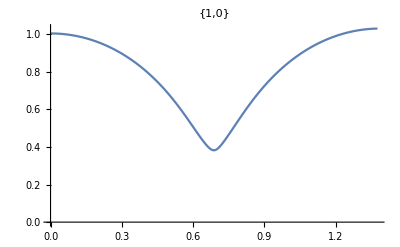
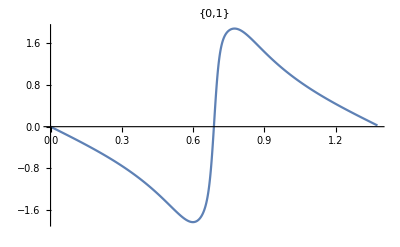
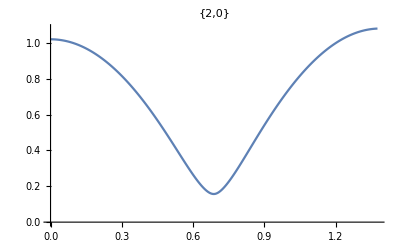
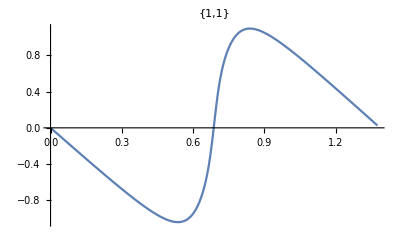
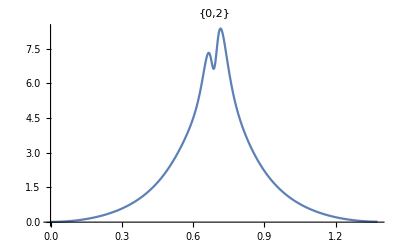
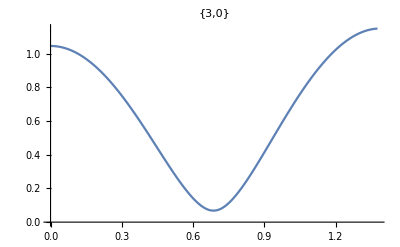
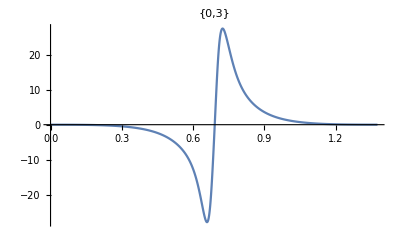
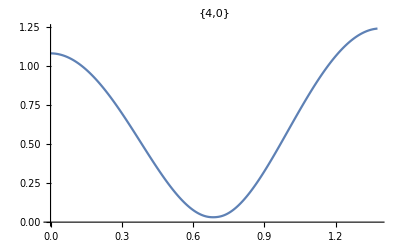

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,sol[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
(* Verify with Monte Carlo *)
Ncases=5000;
cases=RandomVariate[RRdPDF,Ncases];
β=2/Rey;
ω2= 2 γ Ca;
Clear[t];
(*myr=ParallelTable[
r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp,r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,1,Ncases}];*)
myr=ParallelTable[
r[t]/.(NDSolve[
{r[t]r''[t]+3/2 r'[t]^2 ==(1/r[t])^(3 γ)-Cp,r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,1,Ncases}];
mydr=Table[
D[myr[[i]],t],{i,1,Ncases}];

Nt=100;ts2=Table[i,{i,0,T,T/Nt}];
ts2=myts;Nt=Length[ts2];
P=Table[Table[{
myr[[j]]/.{t->ts2[[i]]},
mydr[[j]]/.{t->ts2[[i]]}},{j,1,Ncases}],
{i,1,Nt}];

nonlinmoments=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;2]]]},{i,1,Nt}],{j,1,Length[ks]}];
```

```mathematica
plts=ParallelTable[
Show[
SmoothDensityHistogram[P[[i]],PlotRange->{{xmin,xmax},{ymin,ymax},All}],
ListPlot[myabscissa[[i]],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]]
,{i,1,Length[P]}];
vid=ListAnimate[plts]
```

```mathematica
Export["~/Desktop/movie.avi",vid]
```

~/Desktop/movie.avi

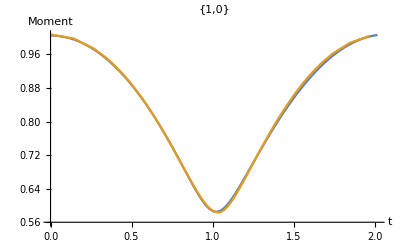
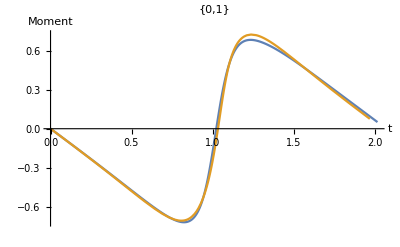
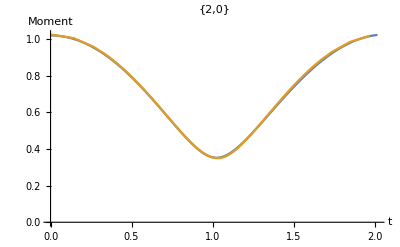
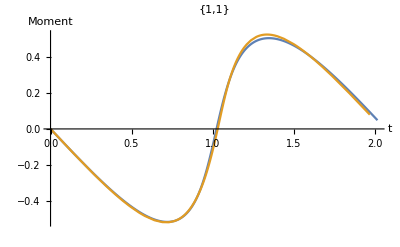
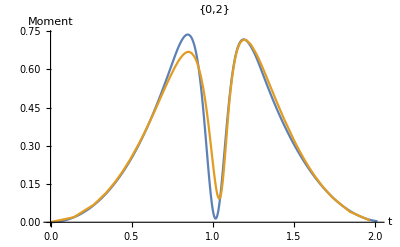
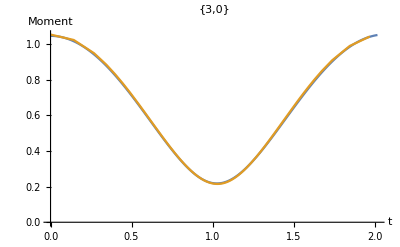
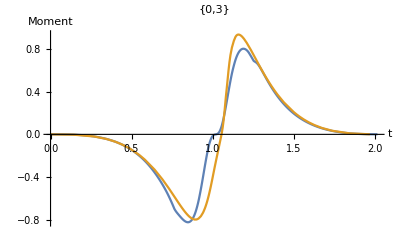

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[{Thread[{ts,sol[[All,i]]}],nonlinmoments[[i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]],AxesLabel->{"t","Moment"}]]
]
,{i,1,Length[moms]}]
plots
```